Kibble-Zurek Scaling in Ising Chain |

Here, the Kibble-Zurek scaling is illustrated for the one-dimensional transverse-field Ising model. See Dziarmaga (2005) and Damski (2005) for details.

Set the energy scale of the model:

```mathematica
$J=1;
```

The Landau-Zener formula: top[n,τ_Q] returns the number of topological excitations after quench of the XXZ chain of length n and quenching parameter τ_Q. The initial state is assumed to be the ground state of the XXZ chain.

```mathematica
Clear[top]
top[n_,τ_]:=Module[
{kk=Range[n-1],
pp},
kk=Pi*N[kk/n];
pp=(2*Pi)*$J*τ*Sin[kk]^2;
Total[Exp[-pp]]
]
```

Here, it is important to notice that only half-integer multiples of 2π/N are allowed for the momentum; k=(2π)/N(n+1/2)  with n=0,1,…,N-1. It corresponds to the anti-periodic boundary condition of the fermion modes, which corresponds to the fermion even parity.

Take  a range of he scaling variable s:=L/√τ_Q:

```mathematica
$ss=PowerRange[2,200,1.25];
```

Calculate the number of topological excitations:

```mathematica
Quiet[
data=Table[{n/Sqrt[t],top[n,t]},{n,20,100,20},{t,n^2/$ss^2}]//N,
General::munfl
];
```

Plot the number of the topological excitations and observe the scaling behavior:

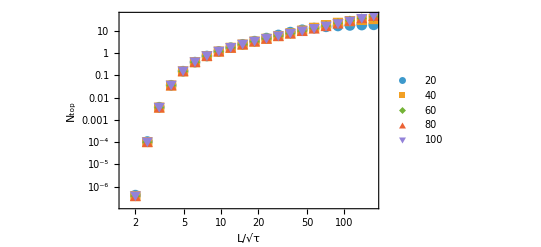

```mathematica
fig1a=ListLogLogPlot[data,
PlotMarkers->Automatic,
PlotLegends->Range[20,100,20],
FrameLabel->{"L/√τ","N_top"}]
```

Note that the number of topological defects drops exponentially for small s:=L/√τ (slow ramping). This is because the momentum can take only half-integer multiples of 2π/N and the energy gap vanishes at no momentum. This means that for any finie size, there always exists the adiabatic limit.

Get the asymptotic behavior:

```mathematica
fig1b=LogLogPlot[x/4,{x,2,200},PlotStyle->{{LightDarkSwitched@Black,Dashed}}];
```

Combine the two plots:

```mathematica
fig=Show[{fig1a,fig1b}]
```

-Graphics-

| Related Guides
▪Quantum Many-Body Systems
▪Q3

| Related Tech Notes
▪A Quantum Playbook
▪Quantum Many-Body Systems with Q3
▪Q3: Quick Start